Make sure that xmin∞ and xmax∞ are such that the potential is vanishing both near the orizon and in the far away region

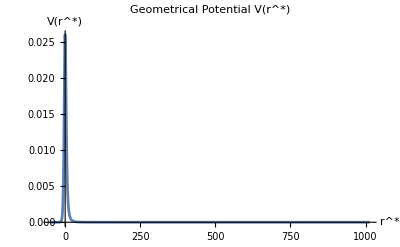

For the values of interest of the regularizing parameter(s) and the minimum and maximum values of ω the function Z_s needs to oscillate enough to ensure that the fit between xmax∞-xfar and xmax∞ and the sampling frequency needs to satisfy the Nyquist–Shannon sampling theorem

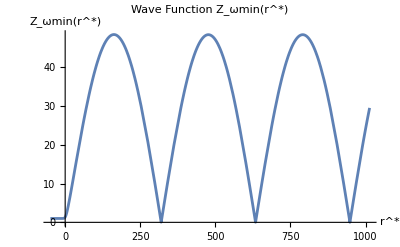

(Γ_(ωmin,))_(0,0)

0.00171226

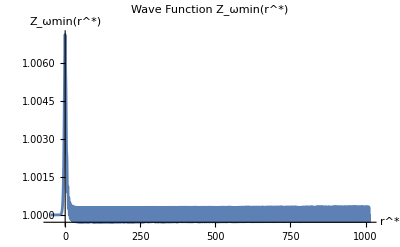

(Γ_(ωmax,))_(0,0)

0.999946

```mathematica
(**    CalibratorGW    **)


Clear["Global`*"]

(*Parameters*)


(*BH parameters*)

M=1; (*Mass of the black hole set to unity*)
Q=0; (*Charge of the BH*)
ℓ=0;(*Regularizing Parameters*)

(*Field parameters*)

s=0; (*Field spin*)
l=0; (*Mode multipole number, l>=s*)


(*Energy table*)
ωj=Table[0.01 j ,{j,1,100}];(*Table of energies where to evaluete the GBF*)



(*The metric*)


(*We will take into account a metric in the form ds^2= -Subscript[g, tt] dt^2 +Subscript[g, rr] dr^2 +Subscript[g, Ω] dΩ^2 where dΩ^2=dθ^2+ Sin[θ]^2 dϕ^2*)

(*Definition of Subscript[g, rr]*)

F[r_]:=Simplify[
(*Schwarzschild*)1-(2 M)/r
(*Reissner-Nordstrom*)(*1-(2 M)/r+Q^2/r^2*)
(*Hayward*)(*1-(2 M r^2)/(r^3+2 M ℓ^2)*)
(*Bardeen*)(*1-(2 M r^2)/((r^2+ℓ^2)^(3/2))*)
(*Simpson-Visser*)(*1-(2 M)/(√(r^2+ℓ^2))*)
(*Peltola-Kunstatter*)(*(r-2 M)/(√(r^2+ℓ^2))*)
(*D’Ambrosio-Rovelli*)(*(1-(2 M)/(√(r^2+ℓ^2)))/(1+ℓ/(√(r^2+ℓ^2)))*)
,{r>=0,ℓ>=0}];

(*Definition of Subscript[g, tt]*)

G[r_]:=Simplify[
(*Schwarzschild*)1-(2 M)/r
(*Reissner-Nordstrom*)(*1-(2 M)/r+Q^2/r^2*)
(*Hatward*)(*1-(2 M r^2)/(r^3+2 M ℓ^2)*)
(*Bardeen*)(*1-(2 M r^2)/((r^2+ℓ^2)^(3/2))*)
(*Simpson-Visser*)(*1-(2 M)/(√(r^2+ℓ^2))*)
(*Peltola-Kunstatter*)(*(r-2 M)/(√(r^2+ℓ^2))*)
(*D’Ambrosio-Rovelli*)(*(1-(2 M)/(√(r^2+ℓ^2)))*)
,{r>=0,ℓ>=0}];

(*Definition of Subscript[g, Ω]*)

H[r_]:=Simplify[
(*tr-Symmetric*)r^2
(*non-tr-Symmetric/Black-Bounces*)(*r^2+ℓ^2*),{r>=0,ℓ>=0}];




(*Numerical inversion of tortoise coordinates*)


 (*Definition of the horizon radius*)

rH=Max[r/.Solve[F[r]==0]];

(*Definition of the tortoise coordinate*)

x[r_]=Re[Integrate[√(1/(F[r] G[r])),r]]; 

(*Numerical inversion*)

(*Near-Horizon sampling*)

nbrr=1000;
tr=N[rH(1+10^Range[-11,-1,(10/(nbrr-1))])];
For[i=1,i<nbrr,i++,X[i]={x[tr[[i]]],tr[[i]]};];
X1=Table[X[nbrr-i],{i,1,nbrr-2}];

(*Far-Horizon sampling*)

For[i=2,i<5000,i++,
X[i]={x[rH(1+0.1i)],rH(1+0.1i)};
]
X2=Table [X[i],{i,2,4999}];


(*Inverted tortoise coordinates*)

XX=Join[X1,X2];(*Inverted tortoise table*)

xmin∞=Min[XX];(*Minimum value of the tortoise coordinate according to the sampling (maximum close to horizon distance according to the sampling)*)
xmax∞=Max[XX];(*Maximum value of the tortoise coordinate according to the sampling (maximum far to horizon distanceaccording to the sampling)*)

r=Interpolation[XX]; (*Inverted tortoise function*)


(*The geometrical potential*)


(*Auxiliary functions*)

DDSqrtH=D[D[√H[r[x]],x],x];
DH=D[H[r[x]],x];
DSqrtGoverH=D[√(G[r[x]]/H[r[x]]),x];
ν=l(l+1)-s(s-1); (*Separation constant*)


(*Geometric potential definition*)

Veff[x_]:=If[s==0,G[r[x]]/H[r[x]] ν+DDSqrtH/(√H[r[x]]),
		If[s==2,G[r[x]]/H[r[x]] ν+(DH)^2/(2 H[r[x]]^2)-DDSqrtH/(√H[r[x]]),
		If[s==1,G[r[x]]/H[r[x]] ν,
		If[s==1/2,G[r[x]]/H[r[x]] ν + √ν DSqrtGoverH]]]];

(*Geometric Potential Plot*)

Print["Make sure that xmin∞ and xmax∞ are such that the potential is vanishing both near the orizon and in the far away region"]
Print[""]
Plot[Veff[x],{x,xmin∞,xmax∞},PlotRange->All,PlotLabel->"Geometrical Potential V(r^*)",AxesLabel->{"r^*","V(r^*)"}](*Gempetrical Potential Plot *)
Print[""]
Print[""]
Print[""]
Print[""]
Print[""]
Print[""]


(*Solving for the GBF*)

	
		ω=ωj[[1]]; (*Frequency of the incoming wave*)

		(*Define the Schrödinger-like equation*)
		schrodingerEq=D[Z[x],{x,2}]+(ω^2-Veff[x]) Z[x]==0;

		(*Boundary conditions for the wavefunction near the horizon*)
		boundaryConditions={Z[xmin∞]==Exp[-I ω (xmin∞)],Z'[xmin∞]==(-I ω)Exp[-I ω (xmin∞)]};

		(*Solve the equation numerically*)
		sol=NDSolve[{schrodingerEq,boundaryConditions},Z,{x,xmin∞,xmax∞}];

Print["For the values of interest of the regularizing parameter(s) and the minimum and maximum values of ω the function Z_s needs to oscillate enough to ensure that the fit between xmax∞-xfar and xmax∞ and the sampling frequency needs to satisfy the Nyquist–Shannon sampling theorem"]
		Print[""]
		Print[""]
		Print[""]
	
		Plot[Evaluate[Abs[Z[x]/. sol]],{x,xmin∞,xmax∞},PlotRange->All,PlotLabel->"Wave Function Z_ωmin(r^*)",AxesLabel->{"r^*","Z_ωmin(r^*)"}]

					(*Far horizon region reconstruction (integration out)*)

					xfar=IntegerPart[xmax∞/4];(*Distance from xmax∞ such that xmax∞-xfar is still in the far region*)

					(*Sampling in the far horizon region*)

							For[
								i=0,i<=xfar,i++,
								p[i]=Z[xmax∞-xfar+i]/. sol
		
								];

					FF=Flatten[Table[p[i],{i,0,xfar}]];(*Table of values of the solution*)
					NLM=NonlinearModelFit[FF,𝒶 Exp[I ω x]+𝒷 Exp[- I ω x],{𝒶,𝒷},x]; (*Fit of the solution *)
					T=1/(Abs[𝒷 /.NLM["BestFitParameters"]])^2;(*GBF value at ωj*)

			

Print[Subscript["Γ_(ωmin,)", s,l]]
T (*GBF Value*)

ω=ωj[[Length[ωj]]]; (*Frequency of the incoming wave*)

		(*Define the Schrödinger-like equation*)
		schrodingerEq=D[Z[x],{x,2}]+(ω^2-Veff[x]) Z[x]==0;

		(*Boundary conditions for the wavefunction near the horizon*)
		boundaryConditions={Z[xmin∞]==Exp[-I ω (xmin∞)],Z'[xmin∞]==(-I ω)Exp[-I ω (xmin∞)]};

		(*Solve the equation numerically*)
		sol=NDSolve[{schrodingerEq,boundaryConditions},Z,{x,xmin∞,xmax∞}];

	
		Plot[Evaluate[Abs[Z[x]/. sol]],{x,xmin∞,xmax∞},PlotRange->All,PlotLabel->"Wave Function Z_ωmin(r^*)",AxesLabel->{"r^*","Z_ωmin(r^*)"}]


					(*Far horizon region reconstruction (integration out)*)

					xfar=IntegerPart[xmax∞/4];(*Distance from xmax∞ such that xmax∞-xfar is still in the far region*)

					(*Sampling in the far horizon region*)

							For[
								i=0,i<=xfar,i++,
								p[i]=Z[xmax∞-xfar+i]/. sol
		
								];

					FF=Flatten[Table[p[i],{i,0,xfar}]];(*Table of values of the solution*)
					NLM=NonlinearModelFit[FF,𝒶 Exp[I ω x]+𝒷 Exp[- I ω x],{𝒶,𝒷},x]; (*Fit of the solution *)
					T=1/(Abs[𝒷 /.NLM["BestFitParameters"]])^2;(*GBF value at ωj*)
			

Print[Subscript["Γ_(ωmax,)", s,l]]
T (*GBF Value*)
```